# Basics of Mathematica

Open the sections for the solutions. [Problems and Solutions by Saulius Valatka]

## Easy Problems

Practicing with input

#### Practice inputting expressions in different forms, e.g. type in the following expressions (preferrably without using the Basic Math Assistant palette):

a^2+b^2

√(a+ⅈ b)

∑_(n=1)^10 (n^2+1)

∫_(-∞)^(+∞) ⅇ^(-λ x^2)ⅆx

(-1 | 0
0 | 1)

∂_x ψ[x]

#### At the same time understand what other ways you can input these expressions: input each one of them without using 2D formatting (i.e. just type them in as text that you could potentially copy to notepad) and in FullForm (i.e. without using any math symbols like + ^ ( ) { }, just heads with arguments, e.g. Power[x, 2], etc.).

Input form:

```mathematica
a^2+b^2;
Sqrt[a+I b];
Sum[n^2+1,{n,1,10}];
Integrate[Exp[-λ x^2],{x,-Infinity,+Infinity}];
{{-1,0},{0,1}};
D[ψ[x],x];
```

FullForm:

```mathematica
Plus[Power[a,2],Power[b,2]];
Sqrt[Complex[a,b]];
Sum[Plus[Power[n,2],1],List[n,1,10]];
Integrate[Exp[Times[-1,λ,Power[x,2]]],List[x,Times[-1,Infinity],Infinity]];
List[List[-1,0],List[0,1]];
D[ψ[x],x];
```

Working with Lists

#### Generate a list of the squares of numbers from 1 to 100

```mathematica
Table[i^2,{i,1,100}]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400,441,484,529,576,625,676,729,784,841,900,961,1024,1089,1156,1225,1296,1369,1444,1521,1600,1681,1764,1849,1936,2025,2116,2209,2304,2401,2500,2601,2704,2809,2916,3025,3136,3249,3364,3481,3600,3721,3844,3969,4096,4225,4356,4489,4624,4761,4900,5041,5184,5329,5476,5625,5776,5929,6084,6241,6400,6561,6724,6889,7056,7225,7396,7569,7744,7921,8100,8281,8464,8649,8836,9025,9216,9409,9604,9801,10000}

#### Replace the head of the List with Plus in order to find the sum of squares

```mathematica
Plus@@Table[i^2,{i,1,100}]
```

338350

#### Construct a 4×4 Vandermonde matrix and find its determinant -Graphics-

```mathematica
V=Table[Subscript[α, i]^j,{i,1,4},{j,0,3}];
V//MatrixForm
```

(1 | α_1 | α_1^2 | α_1^3
1 | α_2 | α_2^2 | α_2^3
1 | α_3 | α_3^2 | α_3^3
1 | α_4 | α_4^2 | α_4^3)

```mathematica
Det[V]//Simplify
```

(α_1-α_2) (α_1-α_3) (α_2-α_3) (α_1-α_4) (α_2-α_4) (α_3-α_4)

Working with expressions

#### Expand (1+a+x)^10, collect in terms of x and simplify each coefficient.

```mathematica
Expand[(1+a+x)^10]
Collect[%,x,Simplify]
```

1+10 a+45 a^2+120 a^3+210 a^4+252 a^5+210 a^6+120 a^7+45 a^8+10 a^9+a^10+10 x+90 a x+360 a^2 x+840 a^3 x+1260 a^4 x+1260 a^5 x+840 a^6 x+360 a^7 x+90 a^8 x+10 a^9 x+45 x^2+360 a x^2+1260 a^2 x^2+2520 a^3 x^2+3150 a^4 x^2+2520 a^5 x^2+1260 a^6 x^2+360 a^7 x^2+45 a^8 x^2+120 x^3+840 a x^3+2520 a^2 x^3+4200 a^3 x^3+4200 a^4 x^3+2520 a^5 x^3+840 a^6 x^3+120 a^7 x^3+210 x^4+1260 a x^4+3150 a^2 x^4+4200 a^3 x^4+3150 a^4 x^4+1260 a^5 x^4+210 a^6 x^4+252 x^5+1260 a x^5+2520 a^2 x^5+2520 a^3 x^5+1260 a^4 x^5+252 a^5 x^5+210 x^6+840 a x^6+1260 a^2 x^6+840 a^3 x^6+210 a^4 x^6+120 x^7+360 a x^7+360 a^2 x^7+120 a^3 x^7+45 x^8+90 a x^8+45 a^2 x^8+10 x^9+10 a x^9+x^10

(1+a)^10+10 (1+a)^9 x+45 (1+a)^8 x^2+120 (1+a)^7 x^3+210 (1+a)^6 x^4+252 (1+a)^5 x^5+210 (1+a)^4 x^6+120 (1+a)^3 x^7+45 (1+a)^2 x^8+10 (1+a) x^9+x^10

#### Generate the sum ∑_(i=1)^5 a_i/b_i and make it have a common denominator.

```mathematica
∑_(i=1)^5 Subscript[a, i]/Subscript[b, i]//Together
```

(a_5 b_1 b_2 b_3 b_4+a_4 b_1 b_2 b_3 b_5+a_3 b_1 b_2 b_4 b_5+a_2 b_1 b_3 b_4 b_5+a_1 b_2 b_3 b_4 b_5)/(b_1 b_2 b_3 b_4 b_5)

#### Given an expression MyLog[∏_(n=1)^5 f[n]], convert it into a sum of MyLogs, i.e. ∑_(n=1)^5 MyLog[f[n]].

```mathematica
Plus@@(MyLog/@(Identity@@MyLog[∏_(n=1)^5 f[n]]))
```

MyLog[f[1]]+MyLog[f[2]]+MyLog[f[3]]+MyLog[f[4]]+MyLog[f[5]]

Functions and patterns

#### Define a function that computes the mean of a list, i.e. MyMean[{1,2,3}] = 2.

```mathematica
MyMean[list_]:=1/Length[list] Plus@@list
```

```mathematica
MyMean[{1,2,3}]
```

2

#### Define a function that squares odd numbers and cubes even numbers.

```mathematica
WeirdFunction[n_?OddQ]:=n^2
WeirdFunction[n_?EvenQ]:=n^3
```

```mathematica
WeirdFunction/@{1,2,3,4}
```

{1,8,9,64}

#### Implement a function FirstAndLast with a pattern match, which does the following: FirstAndLast[a,b,c,d, ..., x,y,z] = {a, z}

```mathematica
FirstAndLast[a_,b___,c_]:={a,c}
```

```mathematica
FirstAndLast[a,b,c,d,x,y,z]
```

{a,z}

#### Expand the expression (1+a+x)^10 and produce a list of terms with odd powers of x.

```mathematica
List@@Collect[Expand[(1+a+x)^10]/.x^(n_?EvenQ)->0,x,Simplify]
```

{(1+a)^10,10 (1+a)^9 x,120 (1+a)^7 x^3,252 (1+a)^5 x^5,120 (1+a)^3 x^7,10 (1+a) x^9}

#### Implement the factorial function recursively. Make sure it can be called only with positive integers and that it performs well.

```mathematica
factorial[0]=1;
factorial[1]=1;
factorial[n_Integer/;n>0]:=factorial[n]=n factorial[n-1]
```

```mathematica
factorial[5]
```

120

#### Implement the simplest case of the system function Riffle (check the documentation for what it does).

```mathematica
?Riffle
```

Riffle[{e_1,e_2,…},x] gives {e_1,x,e_2,x,…}. 
Riffle[{e_1,e_2,…},{x_1,x_2,…}] gives {e_1,x_1,e_2,x_2,…}. 
Riffle[list,x,n] yields a list in which every n^th element is x. 
Riffle[list,x,{i_min,i_max,n}] yields a list in which x appears if possible at positions i_min, i_min+n, i_min+2n, … , i_max.

```mathematica
MyRiffle[l_List,x_]:=Flatten[{#,x}&/@l]
```

```mathematica
MyRiffle[{Subscript[e, 1],Subscript[e, 2],Subscript[e, 3]},x]
```

{e_1,x,e_2,x,e_3,x}

Basic Math

#### Do a series expansion of the exponent to third order and plot the expansion vs. the real function.

```mathematica
srs=Series[Exp[x],{x,0,3}]//Normal
```

1+x+x^2/2+x^3/6

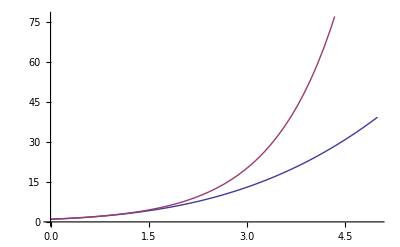

```mathematica
Plot[{srs,Exp[x]},{x,0,5}]
```

#### Plot a 3D parabola.

```mathematica
Plot3D[{x^2+y^2},{x,-10,10},{y,-10,10}]
```

-Graphics3D-

#### Plot the real and imaginary parts of the function √(x^2-1)on the complex plane.

```mathematica
ComplexPlot[f_Function,part_,title_]:=Plot3D[part[√(f[a+b I]^2-1)],{a,-2,2},{b,-2,2},AxesLabel->{"Re", "Im"},PlotLabel->title]
```

```mathematica
{ComplexPlot[√(#^2-1)&,Re,"Real Part"],ComplexPlot[√(#^2-1)&,Im,"Imaginary Part"]}
```

{-Graphics3D-,-Graphics3D-}

#### Construct a set of 5 linear equations with variables x[i] and unspecified coefficients a[i, j]. Solve the equations for x[i].

```mathematica
Solve[Table[a[0,j]+Sum[a[i,j]x[j],{i,0,5}]==0,{j,5}],Table[x[i],{i,5}]]
```

{{x[1]→-a[0,1]/(a[0,1]+a[1,1]+a[2,1]+a[3,1]+a[4,1]+a[5,1]),x[2]→-a[0,2]/(a[0,2]+a[1,2]+a[2,2]+a[3,2]+a[4,2]+a[5,2]),x[3]→-a[0,3]/(a[0,3]+a[1,3]+a[2,3]+a[3,3]+a[4,3]+a[5,3]),x[4]→-a[0,4]/(a[0,4]+a[1,4]+a[2,4]+a[3,4]+a[4,4]+a[5,4]),x[5]→-a[0,5]/(a[0,5]+a[1,5]+a[2,5]+a[3,5]+a[4,5]+a[5,5])}}

#### Implement the dot product function of relativistic vectors {x_0,x_1,x_2,x_3}. Construct a Lorentz transformation matrix (in the x_0-x_1 plane) and show that it preserves the dot product.

```mathematica
SpecialDot[v1_List,v2_List]:=v1.(IdentityMatrix[4]//ReplacePart[#,{1,1}->-1]&).v2
```

```mathematica
SpecialDot[{Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},{Subscript[y, 0],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]}]
```

-x_0 y_0+x_1 y_1+x_2 y_2+x_3 y_3

```mathematica
β[v_]:=v/c
γ[v_]:=(1-β[v]^2)^(-1/2)
```

```mathematica
Lorentz[v_]:=({{γ[v], -γ[v]β[v], 0, 0}, {-γ[v]β[v], γ[v], 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})
```

```mathematica
SpecialDot[(Lorentz[v]//Transpose).{Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},Lorentz[v].{Subscript[y, 0],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]}]
```

(-(v x_0)/(c √(1-v^2/c^2))+x_1/(√(1-v^2/c^2))) (-(v y_0)/(c √(1-v^2/c^2))+y_1/(√(1-v^2/c^2)))+(-x_0/(√(1-v^2/c^2))+(v x_1)/(c √(1-v^2/c^2))) (y_0/(√(1-v^2/c^2))-(v y_1)/(c √(1-v^2/c^2)))+x_2 y_2+x_3 y_3

```mathematica
Simplify[%]
```

-x_0 y_0+x_1 y_1+x_2 y_2+x_3 y_3

## Medium and harder problems

#### Generate a 2×2 matrix whose entries are Random numbers between 0 and 1. Compute the average of the squares of its two Eigenvalues Λ=(λ_1^2+λ_2^2)/2.

```mathematica
Λ:=Mean@(#^2&/@Eigenvalues@Table[Random[],{i,2},{j,2}])
```

```mathematica
Table[Λ,{i,10}]
```

{0.85741,0.479572,0.544709,0.622162,1.0202,0.295597,0.909861,0.989754,0.465278,1.78826}

#### Repeat the computation a few thousand times and Plot a Histogram of the Λs obtained. Compute the average of Λ.

```mathematica
λs:=Table[Λ,{i,5000}];
```

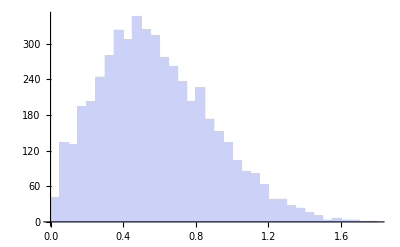
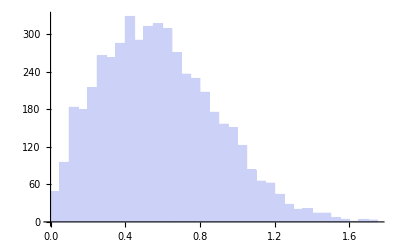
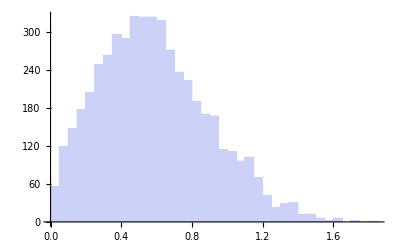
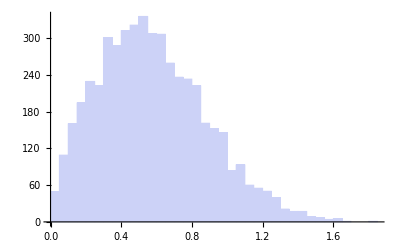
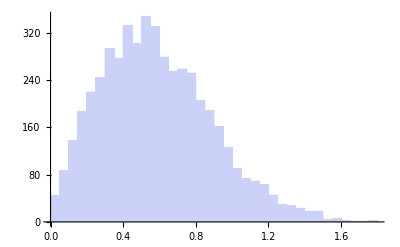

```mathematica
Table[Histogram[λs],{j,5}]
```

```mathematica
Table[Mean[λs],{j,5}]
```

{0.581103,0.580438,0.58571,0.585945,0.581961}

#### Generalize the previous computations to matrices of arbitrary size M. Plot the dependence of ⟨Λ⟩ on M. Do a polynomial fit on the dependence.

```mathematica
ClearAll[Λ];
Λ[M_]:=Mean@(#^2&/@Eigenvalues@Table[Random[],{i,M},{j,M}])
```

```mathematica
AvgΛ[M_]:=AvgΛ[M]=Mean[Table[Λ[M],{j,1000}]]
```

```mathematica
points=Table[{M,AvgΛ[M]},{M,2,30}]//Chop
```

{{2,0.595471},{3,0.84165},{4,1.08567},{5,1.33657},{6,1.58147},{7,1.82702},{8,2.09363},{9,2.32704},{10,2.57397},{11,2.82597},{12,3.07785},{13,3.35441},{14,3.58497},{15,3.83273},{16,4.08491},{17,4.34408},{18,4.5779},{19,4.83242},{20,5.0946},{21,5.33256},{22,5.58648},{23,5.84894},{24,6.10188},{25,6.33685},{26,6.59836},{27,6.812},{28,7.07241},{29,7.32984},{30,7.57837}}

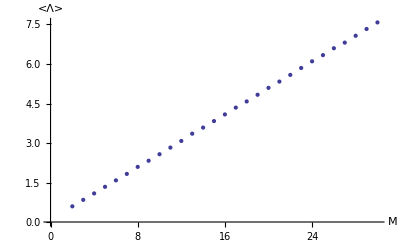

```mathematica
plot=ListPlot[points,AxesLabel->{"M","<Λ>"}]
```

No need for a polynomial fit, it’s obviously linear. Bonus problem: can you find the coefficient analytically ?

```mathematica
fit=Fit[points,x,x]
```

0.254096 x

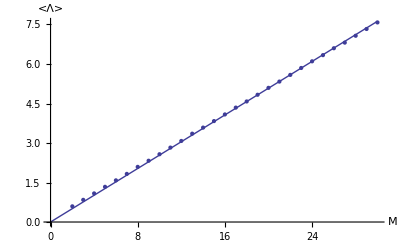

```mathematica
Show[plot, Plot[fit,{x,0,30}]]
```

#### Implement the algebra of creation and anihilation operators for a single 1D harmonic oscillator. Implement a normal ordering operation.

```mathematica
ClearAll[CenterDot]
SetAttributes[CenterDot,{Flat,OneIdentity}]
```

```mathematica
ConstQ[expr_]:=FreeQ[expr,a|ad]
```

```mathematica
h___·(a_+b_)·t___:=h·a·t+h·b·t
h__·c_?ConstQ·t__:=c CenterDot[h,t]
c_?ConstQ·e_:=c e
e_·c_?ConstQ:=c e
```

```mathematica
Nice[expr_]:=expr/.{a->OverHat[a],ad->Superscript[OverHat[a],†]}
```

```mathematica
NormalOrder[expr_]:=expr//.a·ad:>ad·a+1
```

Test it out:

```mathematica
a·ad·a·ad//NormalOrder//Nice
```

1+3 (â)^†·â+(â)^†·(â)^†·â·â

#### Represent states of the oscillator by Ket[n], where n is the mode number. Implement a function that would act on a given state with a given operator. States can be linear combinations of Kets and operators can also be linear combinations of creation and anihilation operators.

Since Ket[0] will be the vacuum, we can immediately set all negative states to zero.

```mathematica
Ket[n_/;n<0]:=0
```

Now we build up the ActOnState function starting from the simplest cases:

```mathematica
ActOnState[a,Ket[n_]]:=√n Ket[n-1]
ActOnState[ad,Ket[n_]]:=√(n+1)Ket[n+1]
ActOnState[ops:CenterDot[__],Ket[n_]]:=Fold[ActOnState[#2,#1]&,Ket[n],Reverse[ops]]
ActOnState[ops_,s:Ket[n_]]:=ops//.{a:>ActOnState[a,s],ad:>ActOnState[ad,s],o:CenterDot[__]:>ActOnState[o,s]}
ActOnState[ops_,expr_]:=expr/.s:Ket[n_]:>ActOnState[ops,s]
```

```mathematica
ActOnState[ad·a+3ad,3Ket[0]+2Ket[1]]//Expand
```

11 1+6 √2 2